```mathematica
e=1000;
NU = 0.25;
c=10;
L=100;
P=80;
cc=Inverse[e/(1-NU^2) ({{1, NU, 0}, {NU, 1, 0}, {0, 0, (1-NU)/2}})] ;
∫_0^L ∫_-c^c ({-3/2(P x y)/c^3,0,-(3 P)/(4 c)(1-(y/c)^2)}.cc .{{-3/2(P x y)/c^3},{0},{-(3 P)/(4 c)(1-(y/c)^2)}})ⅆxⅆy//N
```

{351380.}

```mathematica
∫_0^L (∫_-c^c ({-3/2(P x y)/c^3,0,0}.cc .{{-3/2(P x y)/c^3},{0},{0}})ⅆy)ⅆx//N
∫_0^L (∫_-c^c ({0,0,-(3 P)/(4 c)(1-(y/c)^2)}.cc .{{0},{0},{-(3 P)/(4 c)(1-(y/c)^2)}})ⅆy)ⅆx//N
```

{3200.}

{96.}

```mathematica
cc .{{-3/2(P x y)/c^3},{0},{0}}
```

{{0.-0.00012 x y},{0.+0.00003 x y},{0.}}

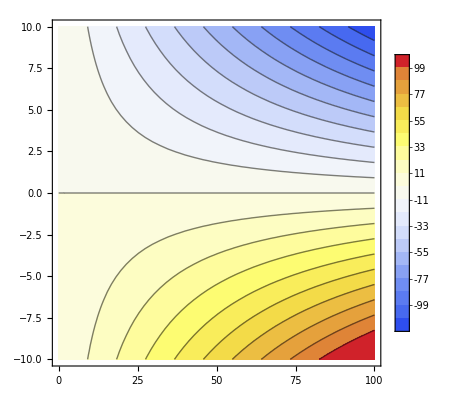

```mathematica
ContourPlot[-3/2(P x y)/c^3,{x,0,L},{y,-c,c},PlotRange->Automatic,ColorFunction->ColorData["TemperatureMap"],PlotLegends->Automatic,Contours->20]
```

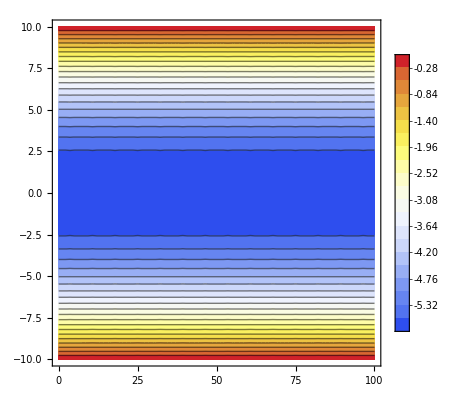

```mathematica
ContourPlot[-(3 P)/(4 c)(1-(y/c)^2),{x,0,L},{y,-c,c},PlotRange->Automatic,ColorFunction->ColorData["TemperatureMap"],PlotLegends->Automatic,Contours->20]
```